```mathematica
ClearAll["Global`*"]
```

### code block below defines functions for mutant invasion fitness given different trade-off assumptions

```mathematica
(*first function v2m[] defines mutant invasion fitness assuming no trade-off *)
s10va[t_?NumericQ,n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,d_]:=ⅇ^(-d t+(a ⅇ^(-t δ) v2eqf1[n-1,tt,τ,tl,a,b,δ,s0,d])/δ)NIntegrate[(ⅇ^(-(a ⅇ^(-δ s) v2eqf1[n-1,tt,τ,tl,a,b,δ,s0,d])/δ+d s) s0)/tl,{s,0,t}]
v200a[s_?NumericQ,n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,d_]:=NIntegrate[ⅇ^(-(a ⅇ^(-δ x) v2eqf1[n-1,tt,τ,tl,a,b,δ,s0,d])/δ+d x),{x,0,s}]
v20a[t_?NumericQ,n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,d_]:=a b  ⅇ^(-τ d)s0 /tl ⅇ^(-(t-τ)δ)NIntegrate[ⅇ^((a ⅇ^(-δ s) v2eqf1[n-1,tt,τ,tl,a,b,δ,s0,d])/δ-d s)v200a[s,n,tt,τ,tl,a,b,δ,s0,d],{s,0,t-τ}]
v2eqf1[n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,d_]:=v2eqf1[n,tt,τ,tl,a,b,δ,s0,d]= v2eqf1[n-1,tt,τ,tl,a,b,δ,s0,d] ⅇ^(-(tt-tl-τ) δ)(v20a[tl+τ,n,tt,τ,tl,a,b,δ,s0,d]+a b ⅇ^(-τ d)  s10va[tl,n,tt,τ,tl,a,b,δ,s0,d]*NIntegrate[ ⅇ^(-(a ⅇ^(-δ (tl+u)) (-1+ⅇ^(δ u)) v2eqf1[n-1,tt,τ,tl,a,b,δ,s0,d])/δ-tl δ-d u),{u,0,tt-tl-τ}])
v2eqf1[0,tt_,τ_,tl_,a_,b_,δ_,s0_,d_]:=v2eqf1[0,tt,τ,tl,a,b,δ,s0,d]=1 
(*code above is for the system dynamics when the resident parasite is at equilibrium if tt-tl > τ*)

v200b[s_?NumericQ,n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,d_]:=NIntegrate[ⅇ^(-(a ⅇ^(-δ x) v2eqf2[n-1,tt,τ,tl,a,b,δ,s0,d])/δ+d x),{x,0,s}]
v2eqf2[n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,d_]:=v2eqf2[n,tt,τ,tl,a,b,δ,s0,d]=a b  ⅇ^(-τ d)s0 /tl ⅇ^(-(tt-τ)δ)v2eqf2[n-1,tt,τ,tl,a,b,δ,s0,d]*NIntegrate[ⅇ^((a ⅇ^(-δ s) v2eqf2[n-1,tt,τ,tl,a,b,δ,s0,d])/δ-d s)v200b[s,n,tt,τ,tl,a,b,δ,s0,d],{s,0,tt-τ}]
v2eqf2[0,tt_,τ_,tl_,a_,b_,δ_,s0_,d_]:=v2eqf2[0,tt,τ,tl,a,b,δ,s0,d]=1
(* code above is for the system dynamics when the resident parasite is at equilibrium if tt-tl<τ - need to use this solution when τ > tt-tl because only parasites that infect hosts from 0<t<tl have enough time to kill their host before the end of the season *)

s10a1[t_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=ⅇ^(-d t+(a ⅇ^(-t δ) ( v2eqf1[n,tt,τ,tl,a,b,δ,s0,d]+v0m))/δ)NIntegrate[(ⅇ^(-(a ⅇ^(-δ s) ( v2eqf1[n,tt,τ,tl,a,b,δ,s0,d]+v0m))/δ+d s) s0)/tl,{s,0,t}]
v2m00a1[s_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=NIntegrate[ⅇ^(d u-(a ⅇ^(-u δ) ( v2eqf1[n,tt,τ,tl,a,b,δ,s0,d]+v0m))/δ) ,{u,0,s}]
v2m0a1[t_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=a b ⅇ^(-τm d)v0m s0/tl ⅇ^(-(t-τm) δ) NIntegrate[ ⅇ^((a ⅇ^(-δ s) ( v2eqf1[n,tt,τ,tl,a,b,δ,s0,d]+v0m))/δ-d s)v2m00a1[s,tt,τ,τm,tl,a,b,δ,s0,v0m,n,d],{s,0,t-τm}]
v2ma1[tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=ⅇ^(-(tt-tl-τm) δ) (v2m0a1[tl+τm,tt,τ,τm,tl,a,b,δ,s0,v0m,n,d]+a b ⅇ^(-τm d)v0m s10a1[tl,tt,τ,τm,tl,a,b,δ,s0,v0m,n,d]*NIntegrate[ⅇ^(-(a ⅇ^(-δ (tl+s)) (-1+ⅇ^(δ s)) ( v2eqf1[n,tt,τ,tl,a,b,δ,s0,d]+v0m))/δ-tl δ-d s),{s,0,tt-tl-τm}])
(* code above is the fitness of a mutant parasite invading a resident population when mutant virulence (τm) is τm<(tt-tl) and resident virulence (τ) is τ<(tt-tl) *)
s10a2[t_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=ⅇ^(-d t+(a ⅇ^(-t δ) ( v2eqf2[n,tt,τ,tl,a,b,δ,s0,d]+v0m))/δ)NIntegrate[(ⅇ^(-(a ⅇ^(-δ s) ( v2eqf2[n,tt,τ,tl,a,b,δ,s0,d]+v0m))/δ+d s) s0)/tl,{s,0,t}]
v2m00a2[s_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=NIntegrate[ⅇ^(d u-(a ⅇ^(-u δ) ( v2eqf2[n,tt,τ,tl,a,b,δ,s0,d]+v0m))/δ) ,{u,0,s}]
v2m0a2[t_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=a b ⅇ^(-τm d)v0m s0/tl ⅇ^(-(t-τm) δ) NIntegrate[ ⅇ^((a ⅇ^(-δ s) ( v2eqf2[n,tt,τ,tl,a,b,δ,s0,d]+v0m))/δ-d s)v2m00a2[s,tt,τ,τm,tl,a,b,δ,s0,v0m,n,d],{s,0,t-τm}]
v2ma2[tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=ⅇ^(-(tt-tl-τm) δ) (v2m0a2[tl+τm,tt,τ,τm,tl,a,b,δ,s0,v0m,n,d]+a b ⅇ^(-τm d)v0m s10a2[tl,tt,τ,τm,tl,a,b,δ,s0,v0m,n,d]*NIntegrate[ⅇ^(-(a ⅇ^(-δ (tl+s)) (-1+ⅇ^(δ s)) ( v2eqf2[n,tt,τ,tl,a,b,δ,s0,d]+v0m))/δ-tl δ-d s),{s,0,tt-tl-τm}])
(* code above is the fitness of a mutant parasite invading a resident population when mutant virulence (τm) is τm<(tt-tl) and resident virulence (τ) is τ>(tt-tl) *)
v2m00b1[s_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=NIntegrate[ⅇ^(d u-(a ⅇ^(-u δ) ( v2eqf1[n,tt,τ,tl,a,b,δ,s0,d]+v0m))/δ) ,{u,0,s}]
v2mb1[tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=a b ⅇ^(-τm d)v0m s0/tl ⅇ^(-(tt-τm) δ) NIntegrate[ ⅇ^((a ⅇ^(-δ s) ( v2eqf1[n,tt,τ,tl,a,b,δ,s0,d]+v0m))/δ-d s)v2m00b1[s,tt,τ,τm,tl,a,b,δ,s0,v0m,n,d],{s,0,tt-τm}]
(* code above is the fitness of a mutant parasite invading a resident population when mutant virulence (τm) is τm>(tt-tl) and resident virulence (τ) is τ<(tt-tl) *)
v2m00b2[s_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=NIntegrate[ⅇ^(d u-(a ⅇ^(-u δ) ( v2eqf2[n,tt,τ,tl,a,b,δ,s0,d]+v0m))/δ) ,{u,0,s}]
v2mb2[tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,b_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=a b ⅇ^(-τm d)v0m s0/tl ⅇ^(-(tt-τm) δ) NIntegrate[ ⅇ^((a ⅇ^(-δ s) ( v2eqf2[n,tt,τ,tl,a,b,δ,s0,d]+v0m))/δ-d s)v2m00b2[s,tt,τ,τm,tl,a,b,δ,s0,v0m,n,d],{s,0,tt-τm}]
(* code above is the fitness of a mutant parasite invading a resident population when mutant virulence (τm) is τm>(tt-tl) and resident virulence (τ) is τ>(tt-tl) *)
(* below sets parameter options so you don't need to specify them each time *)
Options[v2ma11]={ n->200,tt->4,τm->1,τ->1,tl->1,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,v0m->1};
With[{ov=OptionValue},v2ma11[OptionsPattern[]]:=v2ma1[ov@tt,ov@τ,ov@τm,ov@tl,ov@a,ov@b,ov@δ,ov@s0,ov@v0m,ov@n,ov@d]]
Options[v2ma22]={ n->200,tt->4,τm->1,τ->1,tl->1,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,v0m->1};
With[{ov=OptionValue},v2ma22[OptionsPattern[]]:=v2ma2[ov@tt,ov@τ,ov@τm,ov@tl,ov@a,ov@b,ov@δ,ov@s0,ov@v0m,ov@n,ov@d]]
Options[v2mb11]={ n->200,tt->4,τm->1,τ->1,tl->1,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,v0m->1};
With[{ov=OptionValue},v2mb11[OptionsPattern[]]:=v2mb1[ov@tt,ov@τ,ov@τm,ov@tl,ov@a,ov@b,ov@δ,ov@s0,ov@v0m,ov@n,ov@d]]
Options[v2mb22]={ n->200,tt->4,τm->1,τ->1,tl->1,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,v0m->1};
With[{ov=OptionValue},v2mb22[OptionsPattern[]]:=v2mb2[ov@tt,ov@τ,ov@τm,ov@tl,ov@a,ov@b,ov@δ,ov@s0,ov@v0m,ov@n,ov@d]]
(*below defines a new function for mutant invasion fitness for all scenarios that uses the options set for each mutant invasion fitness scenario, and calls the correct invasion fitness depending on the season length (tt), host emergence period length (tl), mutant virulence (τm) and resident virulence (τ) *)
Options[v2m]={v2ma11->All,v2ma22->All,v2mb11->All,v2mb22->All};
v2m[ttt_?NumericQ,tl00_?NumericQ,τm0_?NumericQ,τ0_?NumericQ,opts:OptionsPattern[{v2ma11,v2ma22,v2mb11,v2mb22}]]:=Which[τm0<(ttt-tl00)&&τ0<(ttt-tl00),v2ma11[Sequence@@FilterRules[{opts},Options[v2ma11]]],τm0<(ttt-tl00)&&(ttt-tl00)≤τ0,v2ma22[Sequence@@FilterRules[{opts},Options[v2ma22]]],(ttt-tl00)≤τm0&&τ0<(ttt-tl00),v2mb11[Sequence@@FilterRules[{opts},Options[v2mb11]]],(ttt-tl00)≤τm0&&(ttt-tl00)≤τ0,v2mb22[Sequence@@FilterRules[{opts},Options[v2mb22]]]]

Options[v2eqf11]={ n->200,tt->4,τm->1,τ->1,tl->1,a->10^-8,b->200,δ->2,d->0.5,s0->10^8};
With[{ov=OptionValue},v2eqf11[OptionsPattern[]]:=v2eqf1[ov@n,ov@tt,ov@τ,ov@tl,ov@a,ov@b,ov@δ,ov@s0,ov@d]]
Options[v2eqf22]={ n->200,tt->4,τm->1,τ->1,tl->1,a->10^-8,b->200,δ->2,d->0.5,s0->10^8};
With[{ov=OptionValue},v2eqf22[OptionsPattern[]]:=v2eqf2[ov@n,ov@tt,ov@τ,ov@tl,ov@a,ov@b,ov@δ,ov@s0,ov@d]]
Options[v2m]={v2eqf11->All,v2eqf22->All};
v2eq[ttt_?NumericQ,tl00_?NumericQ,τ0_?NumericQ,opts:OptionsPattern[{v2eqf11,v2eqf22}]]:=Which[τ0<(ttt-tl00),v2eqf11[Sequence@@FilterRules[{opts},Options[v2eqf11]]],(ttt-tl00)≤τ0,v2eqf22[Sequence@@FilterRules[{opts},Options[v2eqf22]]]]

(*second function v2ml[] defines mutant invasion fitness assuming a trade-off where the number of new parasites released upon host death (b) increases linearly with the time between host infection and host death (τ)*)
bx[τ_,v_]:=v(τ+0.5)
s10val[t_?NumericQ,n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,d_]:=ⅇ^(-d t+(a ⅇ^(-t δ) v2eqf1l[n-1,tt,τ,tl,a,v,δ,s0,d])/δ)NIntegrate[(ⅇ^(-(a ⅇ^(-δ s) v2eqf1l[n-1,tt,τ,tl,a,v,δ,s0,d])/δ+d s) s0)/tl,{s,0,t}]
v200al[s_?NumericQ,n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,d_]:=NIntegrate[ⅇ^(-(a ⅇ^(-δ x) v2eqf1l[n-1,tt,τ,tl,a,v,δ,s0,d])/δ+d x),{x,0,s}]
v20al[t_?NumericQ,n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,d_]:=a bx[τ,v]  ⅇ^(-τ d)s0 /tl ⅇ^(-(t-τ)δ)NIntegrate[ⅇ^((a ⅇ^(-δ s) v2eqf1l[n-1,tt,τ,tl,a,v,δ,s0,d])/δ-d s)v200al[s,n,tt,τ,tl,a,v,δ,s0,d],{s,0,t-τ}]
v2eqf1l[n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,d_]:=v2eqf1l[n,tt,τ,tl,a,v,δ,s0,d]=v2eqf1l[n-1,tt,τ,tl,a,v,δ,s0,d] ⅇ^(-(tt-tl-τ) δ)(v20al[tl+τ,n,tt,τ,tl,a,v,δ,s0,d]+a bx[τ,v] ⅇ^(-τ d)  s10val[tl,n,tt,τ,tl,a,v,δ,s0,d]*NIntegrate[ ⅇ^(-(a ⅇ^(-δ (tl+u)) (-1+ⅇ^(δ u)) v2eqf1l[n-1,tt,τ,tl,a,v,δ,s0,d])/δ-tl δ-d u),{u,0,tt-tl-τ}])
v2eqf1l[0,tt_,τ_,tl_,a_,v_,δ_,s0_,d_]:=v2eqf1l[0,tt,τ,tl,a,v,δ,s0,d]=1

v200bl[s_?NumericQ,n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,d_]:=NIntegrate[ⅇ^(-(a ⅇ^(-δ x) v2eqf2l[n-1,tt,τ,tl,a,v,δ,s0,d])/δ+d x),{x,0,s}]
v2eqf2l[n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,d_]:=v2eqf2l[n,tt,τ,tl,a,v,δ,s0,d]=a bx[τ,v]  ⅇ^(-τ d)s0 /tl ⅇ^(-(tt-τ)δ)v2eqf2l[n-1,tt,τ,tl,a,v,δ,s0,d]*NIntegrate[ⅇ^((a ⅇ^(-δ s) v2eqf2l[n-1,tt,τ,tl,a,v,δ,s0,d])/δ-d s)v200bl[s,n,tt,τ,tl,a,v,δ,s0,d],{s,0,tt-τ}]
v2eqf2l[0,tt_,τ_,tl_,a_,v_,δ_,s0_,d_]:=v2eqf2l[0,tt,τ,tl,a,v,δ,s0,d]=1


s10a1l[t_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=ⅇ^(-d t+(a ⅇ^(-t δ) ( v2eqf1l[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ)NIntegrate[(ⅇ^(-(a ⅇ^(-δ s) ( v2eqf1l[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ+d s) s0)/tl,{s,0,t}]
v2m00a1l[s_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=NIntegrate[ⅇ^(d u-(a ⅇ^(-u δ) ( v2eqf1l[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ) ,{u,0,s}]
v2m0a1l[t_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=a bx[τm,v] ⅇ^(-τm d)v0m s0/tl ⅇ^(-(t-τm) δ) NIntegrate[ ⅇ^((a ⅇ^(-δ s) ( v2eqf1l[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ-d s)v2m00a1l[s,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d],{s,0,t-τm}]
v2ma1l[tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=ⅇ^(-(tt-tl-τm) δ) (v2m0a1l[tl+τm,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d]+a bx[τm,v] ⅇ^(-τm d)v0m s10a1l[tl,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d]*NIntegrate[ⅇ^(-(a ⅇ^(-δ (tl+s)) (-1+ⅇ^(δ s)) ( v2eqf1l[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ-tl δ-d s),{s,0,tt-tl-τm}])
s10a2l[t_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=ⅇ^(-d t+(a ⅇ^(-t δ) ( v2eqf2l[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ)NIntegrate[(ⅇ^(-(a ⅇ^(-δ s) ( v2eqf2l[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ+d s) s0)/tl,{s,0,t}]
v2m00a2l[s_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=NIntegrate[ⅇ^(d u-(a ⅇ^(-u δ) ( v2eqf2l[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ) ,{u,0,s}]
v2m0a2l[t_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=a bx[τm,v] ⅇ^(-τm d)v0m s0/tl ⅇ^(-(t-τm) δ) NIntegrate[ ⅇ^((a ⅇ^(-δ s) ( v2eqf2l[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ-d s)v2m00a2l[s,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d],{s,0,t-τm}]
v2ma2l[tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=ⅇ^(-(tt-tl-τm) δ) (v2m0a2l[tl+τm,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d]+a bx[τm,v] ⅇ^(-τm d)v0m s10a2l[tl,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d]*NIntegrate[ⅇ^(-(a ⅇ^(-δ (tl+s)) (-1+ⅇ^(δ s)) ( v2eqf2l[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ-tl δ-d s),{s,0,tt-tl-τm}])
v2m00b1l[s_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=NIntegrate[ⅇ^(d u-(a ⅇ^(-u δ) ( v2eqf1l[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ) ,{u,0,s}]
v2mb1l[tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=a bx[τm,v] ⅇ^(-τm d)v0m s0/tl ⅇ^(-(tt-τm) δ) NIntegrate[ ⅇ^((a ⅇ^(-δ s) ( v2eqf1l[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ-d s)v2m00b1l[s,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d],{s,0,tt-τm}]
v2m00b2l[s_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=NIntegrate[ⅇ^(d u-(a ⅇ^(-u δ) ( v2eqf2l[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ) ,{u,0,s}]
v2mb2l[tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=a bx[τm,v] ⅇ^(-τm d)v0m s0/tl ⅇ^(-(tt-τm) δ) NIntegrate[ ⅇ^((a ⅇ^(-δ s) ( v2eqf2l[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ-d s)v2m00b2l[s,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d],{s,0,tt-τm}]

Options[v2ma11l]={ n->200,tt->4,τm->1,τ->1,tl->1,a->10^-8,v->6.6*15,δ->2,d->0.5,s0->10^8,v0m->1};
With[{ov=OptionValue},v2ma11l[OptionsPattern[]]:=v2ma1l[ov@tt,ov@τ,ov@τm,ov@tl,ov@a,ov@v,ov@δ,ov@s0,ov@v0m,ov@n,ov@d]]
Options[v2ma22l]={ n->200,tt->4,τm->1,τ->1,tl->1,a->10^-8,v->6.6*15,δ->2,d->0.5,s0->10^8,v0m->1};
With[{ov=OptionValue},v2ma22l[OptionsPattern[]]:=v2ma2l[ov@tt,ov@τ,ov@τm,ov@tl,ov@a,ov@v,ov@δ,ov@s0,ov@v0m,ov@n,ov@d]]
Options[v2mb11l]={ n->200,tt->4,τm->1,τ->1,tl->1,a->10^-8,v->6.6*15,δ->2,d->0.5,s0->10^8,v0m->1};
With[{ov=OptionValue},v2mb11l[OptionsPattern[]]:=v2mb1l[ov@tt,ov@τ,ov@τm,ov@tl,ov@a,ov@v,ov@δ,ov@s0,ov@v0m,ov@n,ov@d]]
Options[v2mb22l]={ n->200,tt->4,τm->1,τ->1,tl->1,a->10^-8,v->6.6*15,δ->2,d->0.5,s0->10^8,v0m->1};
With[{ov=OptionValue},v2mb22l[OptionsPattern[]]:=v2mb2l[ov@tt,ov@τ,ov@τm,ov@tl,ov@a,ov@v,ov@δ,ov@s0,ov@v0m,ov@n,ov@d]]
Options[v2ml]={v2ma11l->All,v2ma22l->All,v2mb11l->All,v2mb22l->All};
v2ml[ttt_?NumericQ,tl00_?NumericQ,τm0_?NumericQ,τ0_?NumericQ,opts:OptionsPattern[{v2ma11l,v2ma22l,v2mb11l,v2mb22l}]]:=Which[τm0<(ttt-tl00)&&τ0<(ttt-tl00),v2ma11l[Sequence@@FilterRules[{opts},Options[v2ma11l]]],τm0<(ttt-tl00)&&(ttt-tl00)≤τ0,v2ma22l[Sequence@@FilterRules[{opts},Options[v2ma22l]]],(ttt-tl00)≤τm0&&τ0<(ttt-tl00),v2mb11l[Sequence@@FilterRules[{opts},Options[v2mb11l]]],(ttt-tl00)≤τm0&&(ttt-tl00)≤τ0,v2mb22l[Sequence@@FilterRules[{opts},Options[v2mb22l]]]]

(*third function v2mi[] defines mutant invasion fitness assuming a trade-off where the number of new parasites released upon host death (b) increases linearly as the time between host infection and host death (τ) decreases *)
bxx[τ_,v_]:=v(-τ+4)
s10vai[t_?NumericQ,n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,d_]:=ⅇ^(-d t+(a ⅇ^(-t δ) v2eqf1i[n-1,tt,τ,tl,a,v,δ,s0,d])/δ)NIntegrate[(ⅇ^(-(a ⅇ^(-δ s) v2eqf1i[n-1,tt,τ,tl,a,v,δ,s0,d])/δ+d s) s0)/tl,{s,0,t}]
v200ai[s_?NumericQ,n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,d_]:=NIntegrate[ⅇ^(-(a ⅇ^(-δ x) v2eqf1i[n-1,tt,τ,tl,a,v,δ,s0,d])/δ+d x),{x,0,s}]
v20ai[t_?NumericQ,n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,d_]:=a bxx[τ,v]  ⅇ^(-τ d)s0 /tl ⅇ^(-(t-τ)δ)NIntegrate[ⅇ^((a ⅇ^(-δ s) v2eqf1i[n-1,tt,τ,tl,a,v,δ,s0,d])/δ-d s)v200ai[s,n,tt,τ,tl,a,v,δ,s0,d],{s,0,t-τ}]
v2eqf1i[n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,d_]:=v2eqf1i[n,tt,τ,tl,a,v,δ,s0,d]=v2eqf1i[n-1,tt,τ,tl,a,v,δ,s0,d] ⅇ^(-(tt-tl-τ) δ)(v20ai[tl+τ,n,tt,τ,tl,a,v,δ,s0,d]+a bxx[τ,v] ⅇ^(-τ d)  s10vai[tl,n,tt,τ,tl,a,v,δ,s0,d]*NIntegrate[ ⅇ^(-(a ⅇ^(-δ (tl+u)) (-1+ⅇ^(δ u)) v2eqf1i[n-1,tt,τ,tl,a,v,δ,s0,d])/δ-tl δ-d u),{u,0,tt-tl-τ}])
v2eqf1i[0,tt_,τ_,tl_,a_,v_,δ_,s0_,d_]:=v2eqf1i[0,tt,τ,tl,a,v,δ,s0,d]=1

v200bi[s_?NumericQ,n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,d_]:=NIntegrate[ⅇ^(-(a ⅇ^(-δ x) v2eqf2i[n-1,tt,τ,tl,a,v,δ,s0,d])/δ+d x),{x,0,s}]
v2eqf2i[n_Integer?Positive,tt_?NumericQ,τ_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,d_]:=v2eqf2i[n,tt,τ,tl,a,v,δ,s0,d]=a bxx[τ,v]  ⅇ^(-τ d)s0 /tl ⅇ^(-(tt-τ)δ)v2eqf2i[n-1,tt,τ,tl,a,v,δ,s0,d]*NIntegrate[ⅇ^((a ⅇ^(-δ s) v2eqf2i[n-1,tt,τ,tl,a,v,δ,s0,d])/δ-d s)v200bi[s,n,tt,τ,tl,a,v,δ,s0,d],{s,0,tt-τ}]
v2eqf2i[0,tt_,τ_,tl_,a_,v_,δ_,s0_,d_]:=v2eqf2i[0,tt,τ,tl,a,v,δ,s0,d]=1


s10a1i[t_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=ⅇ^(-d t+(a ⅇ^(-t δ) ( v2eqf1i[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ)NIntegrate[(ⅇ^(-(a ⅇ^(-δ s) ( v2eqf1i[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ+d s) s0)/tl,{s,0,t}]
v2m00a1i[s_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=NIntegrate[ⅇ^(d u-(a ⅇ^(-u δ) ( v2eqf1i[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ) ,{u,0,s}]
v2m0a1i[t_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=a bxx[τm,v] ⅇ^(-τm d)v0m s0/tl ⅇ^(-(t-τm) δ) NIntegrate[ ⅇ^((a ⅇ^(-δ s) ( v2eqf1i[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ-d s)v2m00a1i[s,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d],{s,0,t-τm}]
v2ma1i[tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=ⅇ^(-(tt-tl-τm) δ) (v2m0a1i[tl+τm,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d]+a bxx[τm,v] ⅇ^(-τm d)v0m s10a1i[tl,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d]*NIntegrate[ⅇ^(-(a ⅇ^(-δ (tl+s)) (-1+ⅇ^(δ s)) ( v2eqf1i[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ-tl δ-d s),{s,0,tt-tl-τm}])
s10a2i[t_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=ⅇ^(-d t+(a ⅇ^(-t δ) ( v2eqf2i[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ)NIntegrate[(ⅇ^(-(a ⅇ^(-δ s) ( v2eqf2i[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ+d s) s0)/tl,{s,0,t}]
v2m00a2i[s_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=NIntegrate[ⅇ^(d u-(a ⅇ^(-u δ) ( v2eqf2i[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ) ,{u,0,s}]
v2m0a2i[t_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=a bxx[τm,v] ⅇ^(-τm d)v0m s0/tl ⅇ^(-(t-τm) δ) NIntegrate[ ⅇ^((a ⅇ^(-δ s) ( v2eqf2i[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ-d s)v2m00a2i[s,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d],{s,0,t-τm}]
v2ma2i[tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=ⅇ^(-(tt-tl-τm) δ) (v2m0a2i[tl+τm,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d]+a bxx[τm,v] ⅇ^(-τm d)v0m s10a2i[tl,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d]*NIntegrate[ⅇ^(-(a ⅇ^(-δ (tl+s)) (-1+ⅇ^(δ s)) ( v2eqf2i[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ-tl δ-d s),{s,0,tt-tl-τm}])
v2m00b1i[s_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=NIntegrate[ⅇ^(d u-(a ⅇ^(-u δ) ( v2eqf1i[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ) ,{u,0,s}]
v2mb1i[tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=a bxx[τm,v] ⅇ^(-τm d)v0m s0/tl ⅇ^(-(tt-τm) δ) NIntegrate[ ⅇ^((a ⅇ^(-δ s) ( v2eqf1i[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ-d s)v2m00b1i[s,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d],{s,0,tt-τm}]
v2m00b2i[s_?NumericQ,tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=NIntegrate[ⅇ^(d u-(a ⅇ^(-u δ) ( v2eqf2i[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ) ,{u,0,s}]
v2mb2i[tt_?NumericQ,τ_?NumericQ,τm_?NumericQ,tl_?NumericQ,a_,v_,δ_,s0_,v0m_,n_Integer?Positive,d_]:=a bxx[τm,v] ⅇ^(-τm d)v0m s0/tl ⅇ^(-(tt-τm) δ) NIntegrate[ ⅇ^((a ⅇ^(-δ s) ( v2eqf2i[n,tt,τ,tl,a,v,δ,s0,d]+v0m))/δ-d s)v2m00b2i[s,tt,τ,τm,tl,a,v,δ,s0,v0m,n,d],{s,0,tt-τm}]

Options[v2ma11i]={ n->200,tt->4,τm->1,τ->1,tl->1,a->10^-8,v->6.6*15,δ->2,d->0.5,s0->10^8,v0m->1};
With[{ov=OptionValue},v2ma11i[OptionsPattern[]]:=v2ma1i[ov@tt,ov@τ,ov@τm,ov@tl,ov@a,ov@v,ov@δ,ov@s0,ov@v0m,ov@n,ov@d]]
Options[v2ma22i]={ n->200,tt->4,τm->1,τ->1,tl->1,a->10^-8,v->6.6*15,δ->2,d->0.5,s0->10^8,v0m->1};
With[{ov=OptionValue},v2ma22i[OptionsPattern[]]:=v2ma2i[ov@tt,ov@τ,ov@τm,ov@tl,ov@a,ov@v,ov@δ,ov@s0,ov@v0m,ov@n,ov@d]]
Options[v2mb11i]={ n->200,tt->4,τm->1,τ->1,tl->1,a->10^-8,v->6.6*15,δ->2,d->0.5,s0->10^8,v0m->1};
With[{ov=OptionValue},v2mb11i[OptionsPattern[]]:=v2mb1i[ov@tt,ov@τ,ov@τm,ov@tl,ov@a,ov@v,ov@δ,ov@s0,ov@v0m,ov@n,ov@d]]
Options[v2mb22i]={ n->200,tt->4,τm->1,τ->1,tl->1,a->10^-8,v->6.6*15,δ->2,d->0.5,s0->10^8,v0m->1};
With[{ov=OptionValue},v2mb22i[OptionsPattern[]]:=v2mb2i[ov@tt,ov@τ,ov@τm,ov@tl,ov@a,ov@v,ov@δ,ov@s0,ov@v0m,ov@n,ov@d]]
Options[v2mi]={v2ma11i->All,v2ma22i->All,v2mb11i->All,v2mb22i->All};
v2mi[ttt_?NumericQ,tl00_?NumericQ,τm0_?NumericQ,τ0_?NumericQ,opts:OptionsPattern[{v2ma11i,v2ma22i,v2mb11i,v2mb22i}]]:=Which[τm0<(ttt-tl00)&&τ0<(ttt-tl00),v2ma11i[Sequence@@FilterRules[{opts},Options[v2ma11i]]],τm0<(ttt-tl00)&&(ttt-tl00)≤τ0,v2ma22i[Sequence@@FilterRules[{opts},Options[v2ma22i]]],(ttt-tl00)≤τm0&&τ0<(ttt-tl00),v2mb11i[Sequence@@FilterRules[{opts},Options[v2mb11i]]],(ttt-tl00)≤τm0&&(ttt-tl00)≤τ0,v2mb22i[Sequence@@FilterRules[{opts},Options[v2mb22i]]]]
```

### following code defines functions (essxx[]) to find ESS τ^*

### When t_l is small, τ^*is long enough that all hosts have finished emerging by the time parasite-induced host death begins (i.e. (T-t_l) > τ^*). As t_l increases, τ^* decreases to the point where optimal parasite-induced host death occurs before all hosts have finished emerging (i.e. (T-t_l) < τ^*). We found where the switch between functions occurrs by trial and error.

#### no trade-off between transmission and virulence need to use essnt[ ] when (T-t_l) > τ^*

```mathematica
fd[tt_?NumericQ,τ_?NumericQ,τme_?NumericQ,tl_?NumericQ,a_,b_,δ_,d_,s0_,v0m_,n_]:=Derivative[0,0,1,0,0,0,0,0,0,0,0][v2ma1][tt,τ,τme,tl,a,b,δ,s0,v0m,n,d]
essnt[tt_?NumericQ,τm0_?NumericQ,tl_?NumericQ,a_,b_,δ_,d_,s0_,v0m_,n_]:=τme/.FindRoot[fd[tt,τme,τme,tl,a,b,δ,d,s0,v0m,n],{τme,τm0},AccuracyGoal->4]
```

need to use essnt2[ ] when (T-t_l) ≤ τ^*

```mathematica
fd2[tt_?NumericQ,τ_?NumericQ,τme_?NumericQ,tl_?NumericQ,a_,b_,δ_,d_,s0_,v0m_,n_]:=Derivative[0,0,1,0,0,0,0,0,0,0,0][v2mb2][tt,τ,τme,tl,a,b,δ,s0,v0m,n,d]
essnt2[tt_?NumericQ,τm0_?NumericQ,tl_?NumericQ,a_,b_,δ_,d_,s0_,v0m_,n_]:=τme/.FindRoot[fd2[tt,τme,τme,tl,a,b,δ,d,s0,v0m,n],{τme,τm0},AccuracyGoal->4]
```

#### transmission ↑, virulence ↓ need to use essl[ ] when (T-t_l) > τ^*

```mathematica
fdl[tt_?NumericQ,τ_?NumericQ,τme_?NumericQ,tl_?NumericQ,a_,v_,δ_,d_,s0_,v0m_,n_]:=Derivative[0,0,1,0,0,0,0,0,0,0,0][v2ma1l][tt,τ,τme,tl,a,v,δ,s0,v0m,n,d]
essl[tt_?NumericQ,τm0_?NumericQ,tl_?NumericQ,a_,v_,δ_,d_,s0_,v0m_,n_]:=τme/.FindRoot[fdl[tt,τme,τme,tl,a,v,δ,d,s0,v0m,n],{τme,τm0},AccuracyGoal->4]
```

need to use essl2[ ] below when (T-t_l) ≤ τ^*

```mathematica
fdl2[tt_?NumericQ,τ_?NumericQ,τme_?NumericQ,tl_?NumericQ,a_,v_,δ_,d_,s0_,v0m_,n_]:=Derivative[0,0,1,0,0,0,0,0,0,0,0][v2mb2l][tt,τ,τme,tl,a,v,δ,s0,v0m,n,d]
essl2[tt_?NumericQ,τm0_?NumericQ,tl_?NumericQ,a_,v_,δ_,d_,s0_,v0m_,n_]:=τme/.FindRoot[fdl2[tt,τme,τme,tl,a,v,δ,d,s0,v0m,n],{τme,τm0},AccuracyGoal->4]
```

transmission ↑, virulence ↑
need to use essi[ ] when (T-t_l) > τ^*

```mathematica
fdi[tt_?NumericQ,τ_?NumericQ,τme_?NumericQ,tl_?NumericQ,a_,v_,δ_,d_,s0_,v0m_,n_]:=Derivative[0,0,1,0,0,0,0,0,0,0,0][v2ma1i][tt,τ,τme,tl,a,v,δ,s0,v0m,n,d]
essi[tt_?NumericQ,τm0_?NumericQ,tl_?NumericQ,a_,v_,δ_,d_,s0_,v0m_,n_]:=τme/.FindRoot[fdi[tt,τme,τme,tl,a,v,δ,d,s0,v0m,n],{τme,τm0},AccuracyGoal->4]
```

need to use essi2[ ] when (T-t_l) ≤ τ^*

```mathematica
fdi2[tt_?NumericQ,τ_?NumericQ,τme_?NumericQ,tl_?NumericQ,a_,v_,δ_,d_,s0_,v0m_,n_]:=Derivative[0,0,1,0,0,0,0,0,0,0,0][v2mb2i][tt,τ,τme,tl,a,v,δ,s0,v0m,n,d]
essi2[tt_?NumericQ,τm0_?NumericQ,tl_?NumericQ,a_,v_,δ_,d_,s0_,v0m_,n_]:=τme/.FindRoot[fdi2[tt,τme,τme,tl,a,v,δ,d,s0,v0m,n],{τme,τm0},AccuracyGoal->4]
```

code below generates data to make the left panel in Figure 1 and the left panel of Figure 3

```mathematica
esslistn=ParallelTable[{ttx,essnt[ttx,ttx-tl,tl,a,b,δ,d,s0,v0m,n]/.{tl->1,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,v0m->1,n->200}},{ttx, 3, 4.5, 0.2}];
```

```mathematica
esslistn=Import["ess_ntftt.mx"];
```

```mathematica
essa=essnt[tt,2,tl,a,b,δ,d,s0,v0m,n]/.{tt->3.2,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,v0m->1,n->200,tl->1}
```

2.14407

```mathematica
essb=essnt[tt,2,tl,a,b,δ,d,s0,v0m,n]/.{tt->4,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,v0m->1,n->200,tl->1}
```

2.93648

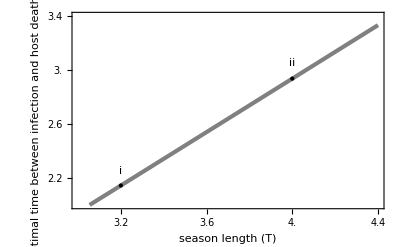

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[2.2,3.4,0.4],None},{{#,#,{0.03,0}}&/@Range[3.2,4.4,0.4],None}};
xx=ListLinePlot[{esslistn},Frame->{{True,True},{True,True}},PlotRange->{{3,4.4},{2,3.4}},FrameTicks->ftrange,PlotStyle->{{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["optimal time between \n infection and host death (τ^*)",16,FontFamily->"Helvetica"],None},{Style["season length (T)",16,FontFamily->"Helvetica"],Style["A",18,FontFamily->"Times"]}},RotateLabel->True,Epilog->{Black,PointSize[Large], Point[{3.2,essa}],Black,PointSize[Large], Point[{4,essb}],Style[Text["i",{3.2,2.25}],18,Italic,FontFamily->"Times"],Style[Text["ii",{4,3.05}],18,Italic,FontFamily->"Times"]}]
```

code below generates data to make the left panel in Figure 2, note that we need to switch from essnt[] to essnt2[] as t_l increases

```mathematica
esslistntf1=ParallelTable[{tlx,essnt[tt,tt-tlx,tlx,a,b,δ,d,s0,v0m,n]/.{tt->3,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,v0m->1,n->200}},{tlx, 0.5, 1.4, 0.1}];
```

```mathematica
esslistntf3=ParallelTable[{tlx,essnt2[tt,2,tlx,a,b,δ,d,s0,v0m,n]/.{tt->3,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,v0m->1,n->200}},{tlx, 1.5, 2.6, 0.1}];
```

```mathematica
esslistntf=Join[esslistntf1,esslistntf3];
```

```mathematica
essc=essnt[tt,2,tl,a,b,δ,d,s0,v0m,n]/.{tt->3,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,v0m->1,n->200,tl->0.8}
```

2.14316

```mathematica
essd=essnt[tt,2,tl,a,b,δ,d,s0,v0m,n]/.{tt->3,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,v0m->1,n->200,tl->1.4}
```

1.59133

```mathematica
esse=essnt2[tt,2,tl,a,b,δ,d,s0,v0m,n]/.{tt->3,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,v0m->1,n->200,tl->2.5}
```

1.73043

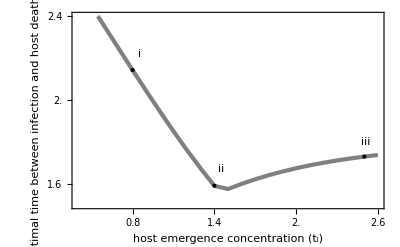

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1.2,2.4,0.4],None},{{#,#,{0.03,0}}&/@Range[0.8,2.6,0.6],None}};
ListLinePlot[{esslistntf},Frame->{{True,True},{True,True}},PlotRange->{{0.4,2.6},{1.5,2.4}},FrameTicks->ftrange,PlotStyle->{{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style[" optimal time between \n infection and host death (τ^*)",16,FontFamily->"Helvetica"],None},{Style["host emergence concentration (t_l)",16,FontFamily->"Helvetica"],Style["A",18,FontFamily->"Times"]}},RotateLabel->True,Epilog->{Black,PointSize[Large], Point[{0.8,essc}],Black,PointSize[Large], Point[{1.4,essd}],Point[{2.5,esse}],Style[Text["i",{0.85,2.22}],18,Italic,FontFamily->"Times"],Style[Text["ii",{1.45,1.67}],18,Italic,FontFamily->"Times"],Style[Text["iii",{2.51,1.8}],18,Italic,FontFamily->"Times"]}]
```

```mathematica
a=10^-8;b=200;δ=2;d=0.5;s0=10^8;
j[t_,tl_]:=If[0<t<tl,1/tl,0];
solx[τ_?NumericQ,tl_?NumericQ,tt_?NumericQ]:=
First@NDSolve[{D[s1[t], t]==s0 j[t,tl]-d s1[t]-a *s1[t]*v1[t],
D[v1[t], t]==-δ v1[t],
D[v2[t], t]== a b*Exp[-d τ]s1[t-τ]*v1[t-τ]-δ v2[t],
s1[t/;t≤0]==0,v1[t/;t≤0]==v0,v2[t/;t≤0]==0},{s1,v1,v2},{t,0,tt},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
```

```mathematica
xtv2b[tx_?NumericQ,tlx_?NumericQ]:=v2[3]/.solx[tx,tlx,3]
```

```mathematica
v01a=v2eqf1[n,tt,τ,tl,a,b,δ,s0,d]/.{tt->3,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,n->200,τ->2.14316448941673,tl->0.8}
```

2.69271×10^9

```mathematica
v02a=v2eqf2[n,tt,τ,tl,a,b,δ,s0,d]/.{tt->3,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,n->200,τ->1.5913319497592384,tl->1.4}
```

1.65778×10^9

```mathematica
v03a=v2eqf2[n,tt,τ,tl,a,b,δ,s0,d]/.{tt->3,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,n->200,τ->1.7304279009979893,tl->2.5}
```

5.72132×10^8

```mathematica
lista1=Table[{v0=v02a;x1=xtv2b[txx,1.4]
},{txx,1,2.9,0.1}];
```

```mathematica
lista2=Table[{v0=v01a;x1=xtv2b[txx,0.8]
},{txx,1,2.9,0.1}];
```

```mathematica
listb2=Table[{v0=v03a;x1=xtv2b[txx,2.5]},{txx,1,2.9,0.1}];
```

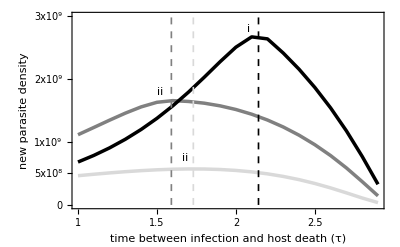

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[5*10^8,3*10^9,5*10^8],None},{{#,#,{0.03,0}}&/@Range[1,3,0.5],None}};
tx=Table[txx,{txx,1,2.9,0.1}];
xx1=Transpose[{Flatten[tx],Flatten[lista1]}];
xx2=Transpose[{Flatten[tx],Flatten[lista2]}];
xx3=Transpose[{Flatten[tx],Flatten[listb2]}];
line1={{1.5913319497592384,0},{1.5913319497592384,3*10^9}};
line2={{2.14316448941673,0},{2.14316448941673,3*10^9}};
line3={{1.7304279009979893,0},{1.7304279009979893,3*10^9}};
discretep=Graphics[{{Gray,AbsoluteThickness[2.5],Line[xx1]},{Black,AbsoluteThickness[2.5],Line[xx2]},{LightGray,AbsoluteThickness[2.5],Line[xx3]},{Gray,Thickness[0.003],Dashed, Line[line1]},{Black,Thickness[0.003],Dashed, Line[line2]},{LightGray,Thickness[0.003],Dashed, Line[line3]}},PlotRangePadding->Scaled[.025],Frame->True,FrameStyle->Directive[Black,Thick],FrameTicks->{{{{0,"0"},{5*10^8,"5x10^8"},{1*10^9,"1x10^9"},{2*10^9,"2x10^9"},{3*10^9,"3x10^9"}},None},{{1,1.5,2,2.5},None}},FrameLabel->{{Style["new parasite density",19,FontFamily->"Helvetica"],None},{Style["time between infection\n and host death (τ)",20,FontFamily->"Helvetica"],Style["B",20,FontFamily->"Times"]}},AspectRatio->1/GoldenRatio,ImageSize->400,FrameTicksStyle->Directive[FontSize->14],Epilog->{Style[Text["i",{2.08,2.8*10^9}],18,Italic,FontFamily->"Times"],Style[Text["ii",{1.52,1.8*10^9}],18,Italic,FontFamily->"Times"],Style[Text["ii",{1.68,7.5*10^8}],18,Italic,FontFamily->"Times"]}]
```

#### code below generates data to make figure 3 which shows the relative percent difference between τ^* with and without each trade-off as season length changes

```mathematica
esslistl=ParallelTable[{ttx,essl[ttx,ttx-tl,tl,a,v,δ,d,s0,v0m,n]/.{tl->1,a->10^-8,v->6.6*15,δ->2,d->0.5,s0->10^8,v0m->1,n->200}},{ttx, 3, 4.5, 0.2}];
```

```mathematica
esslisti=ParallelTable[{ttx,essi[ttx,ttx-tl,tl,a,v,δ,d,s0,v0m,n]/.{tl->1,a->10^-8,v->6.6*15,δ->2,d->0.5,s0->10^8,v0m->1,n->200}},{ttx, 3, 4.5, 0.2}];
```

```mathematica
esslistire1=MapThread[f,{esslisti,esslistn}];
```

```mathematica
esslistdre1=MapThread[f,{esslistl,esslistn}];
```

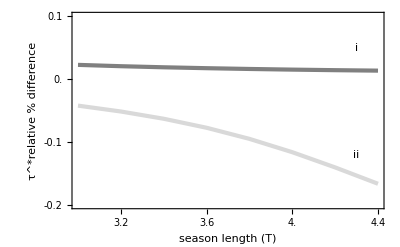

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[-0.2,0.1,0.1],None},{{#,#,{0.03,0}}&/@Range[3.2,4.4,0.4],None}};
retf1=ListLinePlot[{esslistdre1,esslistire1},Frame->{{True,False},{True,False}},PlotRange->{{3,4.4},{-0.2,0.1}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotStyle->{{Gray,AbsoluteThickness[3]},{LightGray,AbsoluteThickness[3]}},(*PlotLegends->Placed[{Style["transmission ↑, virulence ↓",14,FontFamily->"Helvetica"],Style["transmission ↑, virulence ↑",14,FontFamily->"Helvetica"]},{0.35,0.2}],*)FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{Style["season length (T)",18,FontFamily->"Helvetica"],Style["τ^*relative % difference",18,FontFamily->"Helvetica"]},RotateLabel->True,Epilog->{Style[Text["i",{4.3,0.05}],18,Italic,FontFamily->"Times"],Style[Text["ii",{4.3,-0.12}],18,Italic,FontFamily->"Times"]}]
```

#### code below generates data to make figure 3 which shows the relative percent difference between τ^* with and without each trade-off as host emergence concentration changes

```mathematica
esslistnitf1=ParallelTable[{tlx,essi[tt,tt-tlx,tlx,a,v,δ,d,s0,v0m,n]/.{tt->3,a->10^-8,v->6.6*15,δ->2,d->0.5,s0->10^8,v0m->1,n->200}},{tlx, 0.5, 1.9, 0.1}];
```

```mathematica
esslistitf2=ParallelTable[{tlx,essi2[tt,tt-tlx,tlx,a,v,δ,d,s0,v0m,n]/.{tt->3,a->10^-8,v->6.6*15,δ->2,d->0.5,s0->10^8,v0m->1,n->200}},{tlx, 2, 2.6, 0.1}];
```

```mathematica
esslistitf=Join[esslistnitf1,esslistitf2];
```

```mathematica
esslistndtf1=ParallelTable[{tlx,essl[tt,tt-tlx,tlx,a,v,δ,d,s0,v0m,n]/.{tt->3,a->10^-8,v->6.6*15,δ->2,d->0.5,s0->10^8,v0m->1,n->200}},{tlx, 0.5, 1.1, 0.1}];
```

```mathematica
esslistndtf2=ParallelTable[{tlx,essl2[tt,2,tlx,a,v,δ,d,s0,v0m,n]/.{tt->3,a->10^-8,v->6.6*15,δ->2,d->0.5,s0->10^8,v0m->1,n->200}},{tlx, 1.2, 2.6, 0.1}];
```

```mathematica
esslistire2=MapThread[f,{esslistitf,esslistntf}];
```

```mathematica
esslistdre2=MapThread[f,{esslistdtf,esslistntf}];
```

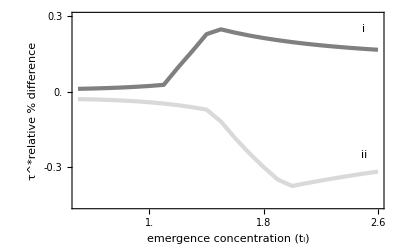

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[-0.6,0.3,0.3],None},{{#,#,{0.03,0}}&/@Range[1,2.6,0.8],None}};
retf2=ListLinePlot[{esslistdre2,esslistire2},Frame->{{True,False},{True,False}},PlotRange->{{0.5,2.6},{-0.45,0.3}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotStyle->{{Gray,AbsoluteThickness[3]},{LightGray,AbsoluteThickness[3]}},(*PlotLegends->Placed[{Style["transmission ↑, virulence ↓",14,FontFamily->"Helvetica"],Style["transmission ↑, virulence ↑",14,FontFamily->"Helvetica"]},{0.35,0.2}],*)FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{Style["emergence concentration (t_l)",18,FontFamily->"Helvetica"],Style["τ^*relative % difference",18,FontFamily->"Helvetica"]},RotateLabel->True,Epilog->{Style[Text["i",{2.5,0.25}],18,Italic,FontFamily->"Times"],Style[Text["ii",{2.5,-0.25}],18,Italic,FontFamily->"Times"]}]
```

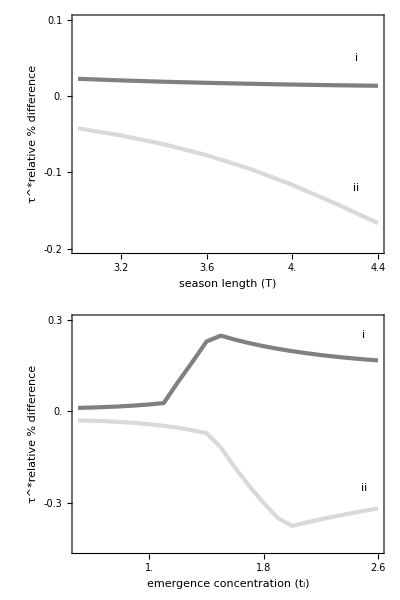

```mathematica
n3=Style[Grid[{{retf1},{retf2}},Spacings->0],ImageSizeMultipliers->{1,1}]
```

#### code below generates plots of the within-season dynamics as shown in the right hand panels of Figure 1

```mathematica
ClearAll["Global`*"]
```

trade-off free model

```mathematica
a=10^-8;b=200;δ=2;d=0.5;s0=10^8;
j[t_,tl_]:=If[0<t<tl,1/tl,0];
solb[τ_?NumericQ,tl_?NumericQ,tt_?NumericQ]:=
First@NDSolve[{D[s1[t], t]==s0 j[t,tl]-d s1[t]-a *s1[t]*v1[t],
D[v1[t], t]==-δ v1[t],
D[v2[t], t]== a b*Exp[-d τ]s1[t-τ]*v1[t-τ]-δ v2[t],
s1[t/;t≤0]==0,v1[t/;t≤0]==v0,v2[t/;t≤0]==0},{s1,v1,v2},{t,0,tt},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
```

host incidence

```mathematica
solc[τ_?NumericQ,tl_?NumericQ,tt_?NumericQ]:=
First@NDSolve[{D[s1[t], t]==s0 j[t,tl]-d s1[t]-a *s1[t]*v1[t],
D[s11x[t], t]==a *s1[t]*v1[t],
D[v1[t], t]==-δ v1[t],
s1[0]==0,s11x[t/;t≤0]==0,v1[0]==v0},{s1,s11x,v1},{t,0,tt},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision];
```

transmission ↑, virulence ↓
the only difference between this code and the code above is the addition of the bx[] trade-off function 
bx[] is a linear trade-off - transmission increases (number of new parasites released at host death) as time to host death increases (virulence decreases)

```mathematica
v=6.6*15;bx[τ_,v_]:=v(τ+0.5)
sold[τ_?NumericQ,tl_?NumericQ,tt_?NumericQ]:=
First@NDSolve[{D[s1[t], t]==s0 j[t,tl]-d s1[t]-a *s1[t]*v1[t],
D[v1[t], t]==-δ v1[t],
D[v2[t], t]== a bx[τ,v]*Exp[-d τ]s1[t-τ]*v1[t-τ]-δ v2[t],
s1[t/;t≤0]==0,v1[t/;t≤0]==v0,v2[t/;t≤0]==0},{s1,v1,v2},{t,0,tt},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
```

transmission ↑, virulence ↑
this code is for the opposite trade-off
bxx[] is again a linear trade-off - transmission increases (number of new parasites released at host death) as time to host death decreases (virulence increases)

```mathematica
bxx[τ_,v_]:=v(-τ+4)
solf[τ_?NumericQ,tl_?NumericQ,tt_?NumericQ]:=
First@NDSolve[{D[s1[t], t]==s0 j[t,tl]-d s1[t]-a *s1[t]*v1[t],
D[v1[t], t]==-δ v1[t],
D[v2[t], t]== a bxx[τ,v]*Exp[-d τ]s1[t-τ]*v1[t-τ]-δ v2[t],
s1[t/;t≤0]==0,v1[t/;t≤0]==v0,v2[t/;t≤0]==0},{s1,v1,v2},{t,0,tt},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
```

#### the following code generates the right hand panel of Figure 1

```mathematica
essa=essnt[tt,2,tl,a,b,δ,d,s0,v0m,n]/.{tt->3.2,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,v0m->1,n->200,tl->1}
```

2.14407

```mathematica
essb=essnt[tt,2,tl,a,b,δ,d,s0,v0m,n]/.{tt->4,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,v0m->1,n->200,tl->1}
```

2.93648

```mathematica
v01=v2eqf1[n,tt,τ,tl,a,b,δ,s0,d]/.{tt->3.2,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,n->200,τ->essa,tl->1}
```

2.06541×10^9

```mathematica
v02=v2eqf1[n,tt,τ,tl,a,b,δ,s0,d]/.{tt->4,a->10^-8,b->200,δ->2,d->0.5,s0->10^8,n->200,τ->essb,tl->1}
```

1.15738×10^9

```mathematica
line1=Line[{{3.2,0},{3.2,100000000}}];
ticks={0,3.2,4};
v0=(v01+v02)/2;
yy2=Plot[{D[s11x[t]/.solc[3,1,4],t]/.t->u/.t->u},{u,0,4},Evaluated->True,PlotRange->{{0,4},{0,100000000}},PlotStyle->{{Darker[Blue],Thickness[0.01]},{Thickness[0.01],Dashing[Medium],Darker[Blue]}},Frame->{True,True,True,False},FrameStyle->Thick,FrameTicks->{{None,None},{{#,#,{0.03,0}}&/@ticks,None}},FrameTicksStyle->Directive[FontSize->20],Epilog->{Directive[Gray, Opacity[0.5],Thickness[0.008]],Dotted,line1}];
```

```mathematica
p1=Evaluate[v2[3.2]/.solb[essa,1,3.2]];
p2=Evaluate[v2[4]/.solb[essb,1,4]];
xx2=Plot[{Evaluate[v2[t]/.solb[essa,1,4]],Evaluate[v2[t]/.solb[essb,1,4]]},{t,0,4},Evaluated->True,PlotRange->{{0,4},{0,2400000000}},PlotStyle->{{LightGray,Thickness[0.01]},{Gray,Thickness[0.01]},{LightGray,Thickness[0.01]},{Gray,Thickness[0.01]}},AxesStyle->Opacity[0],Axes->False,Frame->{True,False,False,True},FrameTicksStyle->Directive[FontSize->20,Opacity[0]],FrameTicks->{{None,None},{{#,#,{0.03,0}}&/@ticks,None}},FrameStyle->Thick,Epilog->{(*Directive[Black,PointSize[0.025]],Point[{3.76,p2}],*)Style[Text["i",{3.1,2100000000}],25,Italic,FontFamily->"Times"],Style[Text["ii",{3.9,1500000000}],25,Italic,FontFamily->"Times"]}];
```

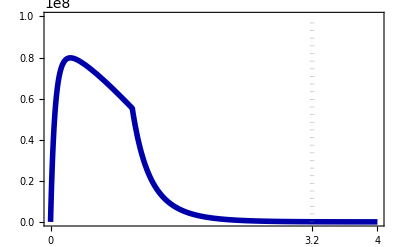
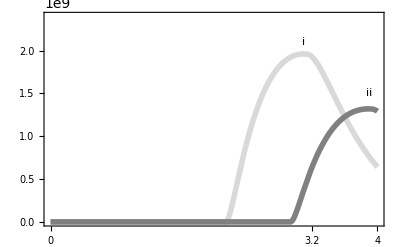
-Graphics--Graphics-timeprogeny densityB incidence rate
(new cases/time)

```mathematica
zz2=Labeled[Overlay[{yy2,xx2}],{Style["time",FontFamily->"Helvetica",FontSize->22],Rotate[Style["progeny density",FontFamily->"Helvetica",FontSize->22],180 Degree],Style["B",FontFamily->"Times",FontSize->22], Style[" incidence rate\n(new cases/time)",FontFamily->"Helvetica",FontSize->22]},{Bottom,Right,Top,Left},RotateLabel->True]
```